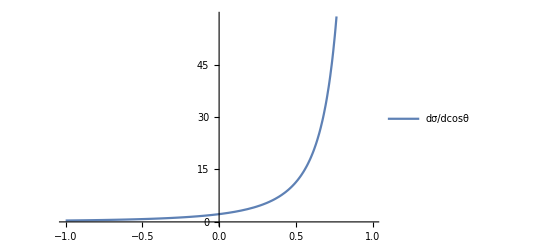

(0.396080624480211135062931490819632428596296731136772797285631966653351101919966053579546855257264
0.80129687820677664973917348315530309006402566151860336615498749303624663243301059587000404427500529
2.2195537662497559511060204563301504052010769178550103571977318353763809892286664938866042058370998
11.336919475097480031321465283882740288224977851446198156758231178991530425772168695421890958736279
2256.88711146755345954271866631678194256008926534625335125470978960843208465821564235587861670614118)

LO1.jpg

```mathematica
Clear[alpha,s,me,mu];
ClearAll["Global`*"];
(*choose precision digits*)
np=100;
(*to micro-barn*)
GevToBarn=SetPrecision[0.3893793721*10^3,np];
alpha=SetPrecision[1/137.03599907430637,np];
Emu = 150;(*GeV*)
(*s=0.405541^2(*Gev^2*)*)
mme=SetPrecision[0.510998928*10^-3,np];
 s=mme^2+mu^2+2*mme*Emu;
me=0(*SetPrecision[0.510998928*10^-3,np]*);(*GeV*)
mu=SetPrecision[105.6583715*10^-3,np];(*GeV*)
t[cthe_]:=(me^2+mu^2-1/2*(((mu^2-me^2)^2)/s+s))*(1-cthe);
u[cthe_]:=2*(mu^2+me^2)-s-(me^2+mu^2-1/2*(((mu^2-me^2)^2)/s+s))*(1-cthe);
u1[t1_]:= 2*(mu^2+me^2)-s-t1;
ppeCM2= (me^2+mu^2-1/2*(((mu^2-me^2)^2)/s+s))/-2;
dsigma0[cthe_]:=GevToBarn*4*Pi*alpha^2/(t[cthe]^2*s)*(s^2/4+u[cthe]^2/4+(mu^2+me^2)*t[cthe]-((mu^2+me^2)^2)/2);
dtsigma0[t1_]:=GevToBarn*4*Pi*1/(2*ppeCM2)*alpha^2/(t1^2*s)*(s^2/4+u1[t1]^2/4+(mu^2+me^2)*t1-((mu^2+me^2)^2)/2);
IM1=Plot[dsigma0[cthe],{cthe,-1,1},PlotLegends->Placed[{dσ/dcosθ},Above],LabelStyle->Directive[Orange,17]]
Table[dsigma0[cthe],{cthe,{-1,-1/2,0,1/2,9602/10000}}]//MatrixForm
Export["LO1.jpg",IM1]
```

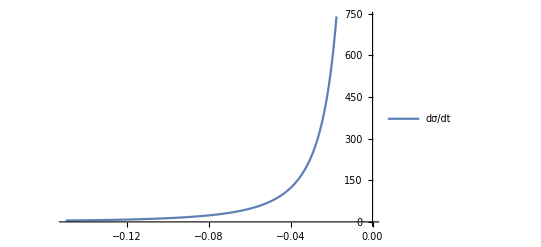

(5.81294163107092917319042185391419603318736529417629862140539282248278679029873497549686268171635304
10.5008364635975620545331780876221374878406939171471747394384082646891028828396515345735728559217737
19.570838963673700714979316095859873351246197926011842145427909145213101722664542726199975327816583
98.6896746944824609602107764353236932121469396140736140449734147768612418336331052163984235808834504
671.307895469414466609754787562849267419807408308306675896775277814306935353317953245490612587841174)

LO2.jpg

```mathematica
IM2=Plot[dtsigma0[t1],{t1,-0.15,0},PlotLegends->Placed[{dσ/dt},Above]]
Table[dtsigma0[t1],{t1,{-14/100,-11/100,-86/1000,-44/1000,212/10000}}]//MatrixForm

Export["LO2.jpg",IM2]
```

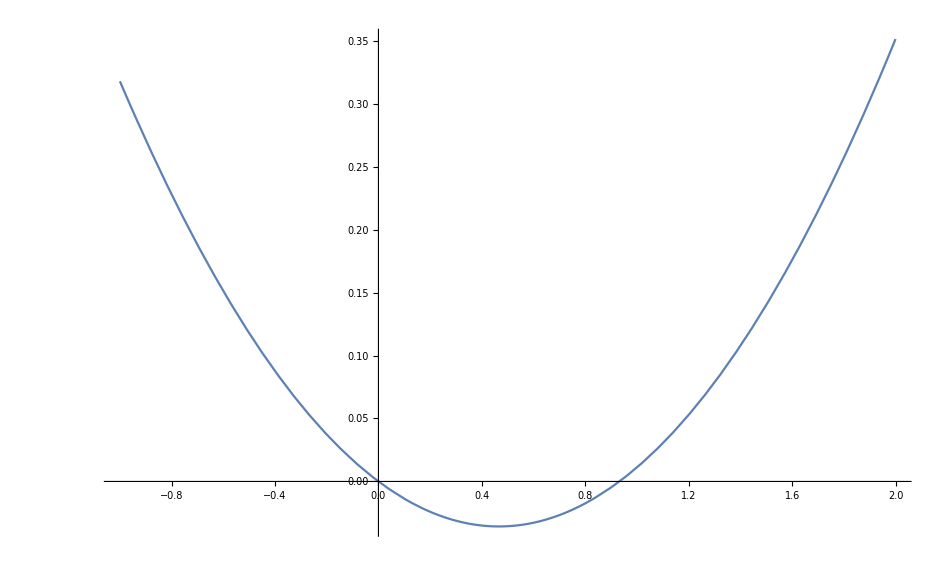

```mathematica
Plot[x^2*s-x*(s-mu^2+mme^2)+mme^2,{x,-1,2}]
```